# NEAT

студент 3 курса 5 группы
Лицкевич Данила
20-12-2020

# NEAT

## 0. Info

https://towardsdatascience.com/neat-an-awesome-approach-to-neuroevolution-3eca5cc7930f

## 1. Individuals

## Generating Population

### Nodes

#### kmActivationFunc

```mathematica
kmActivationFunc[id_]:=
Switch[id,
0, #&,
1,Tanh[#]&,
2,LogisticSigmoid[#]&,
3,Sin[#]&,
4,UnitStep[#]&,
5,Ramp[#]&
]
```

#### kmNode

Input — нейрон входа ;
Output — нейрон выхода;
weight — вес скрытых нейронов ;
enabled — активирована ли связь;
inovation — появление ;

```mathematica
ClearAll[kmNode]
kmNode[id_,layer_,totalFuncs_:5]:=<|
"nodeId"->id,
"layer"->layer,
"inputSum"->0,
"bias"->RandomReal[{-1,1}],
"activationFunc"->RandomInteger[totalFuncs],
"output"->0
|>
```

```mathematica
kmNodeOutput[node_,prevNodes_]:=
Join[node,<|"inputSum"->#,"output"->node["bias"]+kmActivationFunc[node["activationFunc"]][#]|>]&[Total[prevNodes⟦All,"output"⟧]]
```

```mathematica
kmNode[1,1]
kmNodeOutput[%,{kmNode[2,1]~Join~<|"output"->12|>,kmNode[3,2]~Join~<|"output"->2|>}]
```

<|nodeId→1,layer→1,inputSum→0,bias→0.646974,activationFunc→4,output→0|>

<|nodeId→1,layer→1,inputSum→14,bias→0.646974,activationFunc→4,output→1.64697|>

### Connections

```mathematica
CantorPairing[x_,y_]:=((x+y)(x+y+1))/2+y
```

#### kmConnection

Input — нейрон входа ;
Output — нейрон выхода;
weight — вес скрытых нейронов ;
enabled — активирована ли связь;
inovation — появление ;

```mathematica
kmConnection[{in_,out_},weight_:1]:=<|
"input"->in,
"output"->out,
"weight"->RandomReal[{-weight,weight}],
"enabled"->True,
"inovation"->CantorPairing[in,out]
|>
```

### Individual

Input and output nodes are not evolved in the node gene list. Hidden nodes can be added or removed.

```mathematica
ClearAll[kmIndividual]
kmIndividual[input_,output_,hidden_:0]:=
<|
"input"->input,
"output"->output,
"total"->input+output,
"fitness"->∞,
"nodes"->Join[
kmNode[#,1,0]&/@Range[input],
kmNode[#,2]&/@(input+Range[output])
],
"connections"->(kmConnection[#]&/@
Flatten[
Outer[
{#1,#2}&,
Range[input],
Range[input+1,input+output]
],1])
|>
```

### Population

Input — количество входов;
Output — количество выходов;

```mathematica
kmPopulation[in_,out_,size_:10,options___]:=<|
"input"->in,
"output"->out,
"best"-><|"fitness"->+∞|>,
"history"->{},
"size"->size,
(*"inovations"->{},*)
"individuals"->Array[kmIndividual[in,out]&,size],
"params"-><|
"addConnRate"->0.8,
"removeConnRate"->0.1,
"addNodeRate"->0.7,
"removeNodeRate"->0.05
|>
|>~Join~options
```

### Tests

```mathematica
testPop=kmPopulation[2,3];
```

## Individual decoding

### Connection' s logics

#### kmFindNode

```mathematica
kmFindNode[individual_,id_]:=
First@FirstPosition[individual["nodes"],<|"nodeId"->id,___|>]
```

```mathematica
kmFindNode[testPop["individuals"]⟦1⟧,3]
```

3

#### kmInNodes

Finds all nodes which are  IN nodes for the node

```mathematica
kmInNodes[nodeId_,connections_]:=
Reap[
If[nodeId==#["output"],Sow[#["input"]]]&/@connections;
]//Last//Last
```

```mathematica
kmInNodes[2,{kmConnection[{1,2}],kmConnection[{3,2}]}]
```

{1,3}

#### kmExistConnectionQ

```mathematica
kmExistConnectionQ[connection:{in_,out_},connections_]:= 
Or@@({#["input"],#["output"]}==connection&/@connections)
```

### Prepare for evaluation

#### kmNodesToLayers

```mathematica
ClearAll[kmNodesToLayers]
kmNodesToLayers[individual_]:=
Module[
{maxLayer=Max[individual[["nodes",All,"layer"]]],
nodes
},
Join[individual,
<|
"maxLayer"->maxLayer,
"nodesLayered"->Function[{layer},Select[individual["nodes"],#["layer"]==layer&]]/@Range[maxLayer]
|>
]
]
```

#### kmIndividualsToLayers

```mathematica
ClearAll[kmIndividualsPrepare]
SetAttributes[kmIndividualsPrepare,HoldFirst]
kmIndividualsPrepare[population_]:=
population⟦"individuals"⟧=kmNodesToLayers[#]&/@population["individuals"]
```

```mathematica
kmIndividualsPrepare[testPop];
```

#### kmInitFirstLayer

```mathematica
ClearAll[kmInitFirstLayer]
kmInitFirstLayer[nodes_,inputs_List]:=
MapThread[Join[#1,<|"output"->#2|>]&,{SortBy[nodes,#["nodeId"]&],inputs}]
```

#### kmGetNodesLayered

```mathematica
ClearAll[kmGetNodesLayered]
kmGetNodesLayered[individual_,nodeIds_]:=
Flatten[Function[{nodeId},Select[individual["nodesLayered"]//Flatten,#["nodeId"]==nodeId&,1]]/@nodeIds]
```

#### kmInNodesLayered

```mathematica
ClearAll[kmInNodesLayered]
kmInNodesLayered[individual_,node_]:=kmGetNodesLayered[individual,kmInNodes[node["nodeId"],individual["connections"]]]
```

```mathematica
kmInNodesLayered[testPop["individuals"][[1]],<|"nodeId"->3,"layer"->1,"inputSum"->0,"bias"->-0.012840107337042994,"activationFunc"->0,"output"->1|>]
```

{<|nodeId→1,layer→1,inputSum→0,bias→-0.601185,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.41802,activationFunc→0,output→0|>}

### Evaluation

#### kmIndividualEvaluate

```mathematica
ClearAll[kmIndividualEvaluate]
kmIndividualEvaluate[individual_,inputs_:{_,_}]:=
Module[
{individualCopy=individual},
individualCopy[["nodesLayered",1]]=kmInitFirstLayer[individualCopy["nodesLayered"]//First,inputs];
Function[{layer},
individualCopy[["nodesLayered",layer]]=
Function[{node},
kmNodeOutput[node,kmInNodesLayered[individualCopy,node]]
]/@individualCopy[["nodesLayered",layer]]
]/@Range[2,individual["maxLayer"]];
kmGetNodesLayered[individualCopy,Range[#+1,#+individual["output"]]&[individual["input"]]]⟦All,"output"⟧
]
```

```mathematica
kmIndividualEvaluate[testPop["individuals"][[1]],{.1,.2}]
```

{-0.39278,0.987973,1.27498}

## Population viewing (realisatoin Delayed)

```mathematica
testIndividual=<|"input"->2,"output"->3,"hidden"->4,"connections"->{<|"input"->1,"output"->5,"weight"->-0.9628618224751473,"enabled"->1,"inovation"->1|>,<|"input"->3,"output"->4,"weight"->0.22393191857363837,"enabled"->1,"inovation"->2|>,<|"input"->4,"output"->6,"weight"->-0.4785485230617863,"enabled"->1,"inovation"->3|>,<|"input"->6,"output"->5,"weight"->0.45075859641862426,"enabled"->1,"inovation"->4|>,<|"input"->8,"output"->5,"weight"->0.5039873848534051,"enabled"->1,"inovation"->5|>}|>;
```

### Individual viewing

#### kmNodes

1  – in node
2  – out node
3  – hidden node

```mathematica
kmNodes[type_,nodesQuant_,layer_]:=
{Switch[type,1,Red,2,Blue,3,Gray,True,Black],Disk[{-nodesQuant+2#,layer},0.25]&/@Range[nodesQuant]}
```

#### kmViewIndividual

```mathematica
kmViewIndividual[individ_]:=
Graphics[{kmNodes[1,3,1],kmNodes[2,2,2]}]
```

```mathematica
Dynamic@kmViewIndividual[1]
```

```mathematica
Graph
```

### Population viewing

## Population operations

### kmAddConnection

```mathematica
SetAttributes[kmAddConnection,HoldFirst]
kmAddConnection[population_,individualId_,conn:{in_,out_}]:= 
Block[{
individual=population["individuals"]⟦individualId⟧
},
individual⟦"connections"⟧=Join[
individual["connections"],
If[individual["nodes"]⟦in,"layer"⟧<individual["nodes"]⟦out,"layer"⟧,{kmConnection[conn]},{}]
];
population⟦"individuals", individualId⟧=kmNodesToLayers[individual]
]
```

### kmAddNode

```mathematica
SetAttributes[kmAddNode,HoldFirst]
kmAddNode[population_,individualId_,connectionId_]:= 
Block[{
individual=population["individuals"]⟦individualId⟧,
connection, oldOutNodePos
},
connection=individual["connections"]⟦connectionId⟧;
individual⟦"connections",connectionId,"enabled"⟧=False;

oldOutNodePos=kmFindNode[individual,connection["output"]];
individual⟦"total"⟧+=1;
individual⟦"nodes"⟧=
Append[individual["nodes"],kmNode[individual["total"],individual⟦"nodes",oldOutNodePos,"layer"⟧]];
individual⟦"nodes",oldOutNodePos,"layer"⟧+=1;

individual⟦"connections"⟧=Join[
{kmConnection[{connection["input"],#}],
kmConnection[{#,connection["output"]}]}&[individual["total"]],
individual["connections"]
];
population⟦"individuals", individualId⟧=kmNodesToLayers[individual]
]
```

### tests

```mathematica
kmAddNode[testPop,1,1]
kmAddConnection[testPop,1,{1,7}]
```

## Population mutations

### kmMutateNodes

```mathematica
SetAttributes[kmMutateNodes,HoldFirst]
kmMutateNodes[population_,individualId_]:= 
If[
RandomReal[]<population["params","addNodeRate"],
kmAddNode[population,individualId,RandomInteger[{1,Length[testPop⟦"individuals",individualId,"connections"⟧]}]]
]
```

### kmMutateConnections

```mathematica
SetAttributes[kmMutateConnections,HoldFirst]
kmMutateConnections[population_,individualId_]:= 
If[
RandomReal[]<population["params","addConnRate"],
kmAddConnection[population,individualId,RandomSample[population[["individuals",individualId,"nodes"]],2]⟦All,"nodeId"⟧]
]
```

### kmCrossover

#### kmNodesFromConns

```mathematica
kmNodesFromConnections[connections_]:= 
Union[Part[connections,All,"input"],Part[connections,All,"output"]]
```

#### kmCrossover

```mathematica
kmCrossover[parent1_,parent2_]:= 
Module[
{conns1,conns2, nodes1,nodes2, 
separator= RandomChoice[
Join[parent1["connections"],parent2["connections"]]
]["inovation"]
},
conns1 =Select[parent1["connections"],#["inovation"]≤separator&] ;
conns2=Select[parent2["connections"],#["inovation"]>separator&];
nodes1=kmNodesFromConnections[conns1];
nodes2=Complement[kmNodesFromConnections[conns2],nodes1];
kmNodesToLayers@<|
"input"->parent1["input"],
"output"->parent1["output"],
"total"->Length[Join[nodes1,nodes2]],
"nodes"->Join[parent1["nodes"]⟦nodes1⟧,parent2["nodes"]⟦nodes2⟧],
"connections"->Join[conns1,conns2]
|>
]
```

```mathematica
kmCrossover[testPop[["individuals",1]],testPop[["individuals",3]]]
```

<|input→2,output→3,total→6,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.601185,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.41802,activationFunc→0,output→0|>,<|nodeId→3,layer→3,inputSum→0,bias→-0.6883,activationFunc→3,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.69666,activationFunc→1,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→0.700542,activationFunc→2,output→0|>,<|nodeId→6,layer→3,inputSum→0,bias→-0.239504,activationFunc→1,output→0|>},connections→{<|input→1,output→6,weight→-0.348151,enabled→False,inovation→34|>,<|input→1,output→3,weight→0.739868,enabled→False,inovation→13|>,<|input→1,output→4,weight→0.427015,enabled→True,inovation→19|>,<|input→1,output→5,weight→0.207454,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.186508,enabled→True,inovation→18|>,<|input→2,output→4,weight→-0.0293899,enabled→True,inovation→25|>,<|input→2,output→5,weight→-0.321011,enabled→True,inovation→33|>},maxLayer→3,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→-0.601185,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.41802,activationFunc→0,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.69666,activationFunc→1,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→0.700542,activationFunc→2,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→-0.6883,activationFunc→3,output→0|>,<|nodeId→6,layer→3,inputSum→0,bias→-0.239504,activationFunc→1,output→0|>}}|>

## Population evolution

### Fitness

#### kmAssessFitnessAll

```mathematica
ClearAll[kmAssessFitnessAll]
SetAttributes[kmAssessFitnessAll,HoldFirst]
kmAssessFitnessAll[population_Symbol,fitness_Function]:=Module[
{min},
min=Min[population[["individuals",All,"fitness"]]=(fitness/@population["individuals"])];

If[min<population["best","fitness"],
AppendTo[population["history"],
population["best"]=population⟦"individuals",Position[population[["individuals",All,"fitness"]],min]⟦1,1⟧⟧
]
]
]
```

#### kmAssessFitness

```mathematica
ClearAll[kmAssessFitness]
SetAttributes[kmAssessFitness,HoldFirst]
kmAssessFitness[population_Symbol,fitness_Function,individualId_]:=Module[
{fit},
fit=population[["individuals",individualId,"fitness"]]=fitness@population[["individuals",individualId]];
If[fit<population["best","fitness"],
AppendTo[population["history"],
population["best"]=population⟦"individuals",individualId⟧
]
]
]
```

### Elimination

```mathematica
SetAttributes[kmElimination,HoldFirst]
kmElimination[population_,replaceIndividual_]:=
Block[{
index=RandomChoice[1/(Exp/@population["fitness"])->Range[population["size"]]]
},
population⟦"individuals",index⟧=replaceIndividual;
]
```

### Selection

```mathematica
SetAttributes[kmSelection,HoldFirst]
kmSelection[population_]:=
RandomChoice[(#/Total[#]&)@(Exp/@population["fitness"])->Range[population["size"]]]
```

### Evolution

```mathematica
SetAttributes[kmEvolveOne,HoldFirst]
kmEvolveOne[population_,fitness_]:=
Catch[
Block[{individualId,save},
kmAssessFitness[population,fitness];
individualId=kmSelection[population];

If[RandomReal[]<population⟦"params","crossOverRate"⟧,

population⟦"state"⟧=population⟦"state"⟧+{1,0,0};
kmElimination[population,#]&[
kmCrossover[population⟦"individuals",individualId⟧,
population⟦"individuals",RandomInteger[{1,population["size"]}]⟧
]];
,
If[
RandomReal[]<population⟦"params","addConnRate"⟧,
population⟦"state"⟧=population⟦"state"⟧+{1,0,0};
kmAddConnection[population,individualId,RandomSample[population[["individuals",individualId,"nodes"]],2]⟦All,"nodeId"⟧];
];
If[
RandomReal[]<population⟦"params","addNodeRate"⟧,
population⟦"state"⟧=population⟦"state"⟧+{0,0,1};
kmAddNode[population,individualId,RandomInteger[{1,Length[population⟦"individuals",individualId,"connections"⟧]}]];
]
];

]
];
```

## Test Task 1 - simple binary Classification in 2D

### kmClassificationTask – generate a task

```mathematica
ClearAll[kmClassificationTask]
kmClassificationTask[function_,testersNumber_:50,rangeX_:{0,6},rangeY_:{-1,1}]:=
Block[{targets,
testers
},
testers =Thread[ {RandomReal[rangeX,testersNumber],RandomReal[rangeY,testersNumber]}];
targets=If[function[#1]>#2,1,0]&@@@testers;
<|"function"->function,"testers"->testers,"targets"->targets,"rangeX"->rangeX, "rangeY"->rangeY|>
]
```

```mathematica
kmClassificationTask[Sin]
```

<|function→Sin,testers→{{0.147236,0.839423},{0.387677,0.898716},{1.27893,-0.719964},{0.358662,0.099178},{1.62834,0.385243},{1.37709,-0.690725},{1.90187,0.586765},{0.835666,-0.443102},{1.26454,-0.47074},{1.1427,0.34159},{1.89169,-0.549811},{1.79415,-0.250978},{0.87983,0.132221},{0.414971,0.364946},{0.338871,-0.287722},{1.04386,0.178351},{1.38899,-0.435712},{1.92182,-0.291332},{1.16475,-0.668415},{1.22563,0.472183},{0.344156,-0.715595},{0.0306463,-0.768185},{1.46484,0.593822},{0.517801,-0.97487},{0.487843,-0.755055},{0.578918,-0.287435},{0.953298,0.420392},{0.670406,0.860388},{1.44215,-0.650961},{0.237755,-0.356611},{1.05215,-0.549437},{0.137801,0.546355},{0.468418,-0.2411},{0.835778,-0.704406},{1.24498,0.384747},{0.586929,0.290845},{1.1125,0.720325},{1.54228,0.198505},{1.74443,0.577402},{1.80272,0.585426},{1.53286,-0.323067},{1.31668,0.158303},{1.21924,-0.893169},{1.76644,0.158151},{1.96435,-0.637323},{0.763811,-0.128601},{0.275526,0.150988},{0.0186867,0.69587},{1.15385,-0.910371},{0.906569,-0.211972}},targets→{0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1},rangeX→{0,2},rangeY→{-1,1}|>

### Additional functions

#### kmPredictionToAnswer

```mathematica
ClearAll[kmPredictionToAnswer]
SetAttributes[kmPredictionToAnswer,Listable]
kmPredictionToAnswer[prediction_]:=If[prediction>0.5,1,0]
```

#### kmClassificationAccuracy

```mathematica
kmClassificationAccuracy[targets_,predictions_]:=N@EuclideanDistance[targets,predictions]
```

#### kmClassificationPredictions

```mathematica
kmClassificationPredictions[task_,individual_]:=LogisticSigmoid[First@kmIndividualEvaluate[individual,#]&/@task["testers"]]
```

#### kmClassificationFitness

```mathematica
kmClassificationFitness[task_]:=With[
{targets=task["targets"],testers=task["testers"]},
Function[{individual},
N@EuclideanDistance[targets,LogisticSigmoid@kmIndividualEvaluate[individual,#]&/@testers]
]
]
```

### kmShowPredictions

#### NonZeroQ

```mathematica
ClearAll[NonZeroQ]
NonZeroQ[n_]:=(n=!=0)&&NumberQ[n]
```

#### kmShowTestersEpilog

```mathematica
ClearAll[kmShowTestersEpilog]
kmShowTestersEpilog[testers_,targets_,predictions_]:=
{AbsolutePointSize[11],{
Red,Point@Extract[testers,Position[targets-#,_?NonZeroQ]],
White,Point@Extract[testers,Position[targets-#,0]]},
AbsolutePointSize[7],{
Darker@Yellow,Point@Extract[testers,Position[#,0]],
Blue,Point@Extract[testers,Position[#,1]]
}
}&[kmPredictionToAnswer[predictions]]
```

#### kmShowPredictions

```mathematica
ClearAll[kmShowPredictions]
kmShowPredictions[task_,predictions_]:=
With[{
function =task["function"]
},
Labeled[
Plot[function[x],{x,Sequence@@task["rangeX"]},
Epilog->kmShowTestersEpilog[task["testers"],task["targets"],predictions],
PlotRange->{task["rangeX"],task["rangeY"]},AspectRatio->1,Axes->True,
Background->LightGray
],
"Error: "<>ToString@kmClassificationAccuracy[task["targets"],predictions]
]

]
```

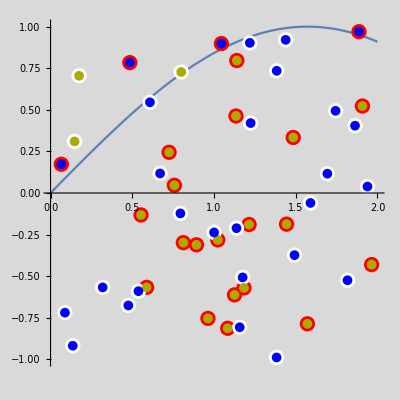
-Graphics-Error: 3.71078

```mathematica
kmShowPredictions[classTest,RandomReal[{0,1},50]]
```

### Test

```mathematica
classTest=kmClassificationTask[Sin];
fitnessClassTest=kmClassificationFitness[classTest];

popClassTest=kmPopulation[2,1];
kmIndividualsPrepare[popClassTest];
fitnessClassTest[#]&/@popClassTest["individuals"]
```

{3.89214,3.02848,2.80359,5.06724,4.46339,5.12116,5.058,5.05428,5.05816,3.72354}

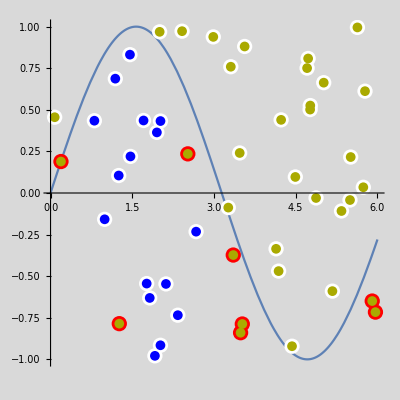
-Graphics-Error: 2.80359

```mathematica
kmShowPredictions[classTest,kmClassificationPredictions[classTest,popClassTest[["individuals",3]]]]
```